```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/hybrid_tail/math

```mathematica
Mpl=2.4 10^18;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10;
```

```mathematica
Π2=100;
μ1=Π2/(M^2 ϕc)
Λ=(5.4 10^15)/Mpl 10/Sqrt[Π2] M Sqrt[ϕc]
ψr=Sqrt[(Λ^4 Sqrt[Π2])/(48Sqrt[2 π^3])]
```

9.77504×10^8

7.19653×10^-7

8.42376×10^-14

### N = 2

```mathematica
ys={y1,y2};
pys={py1,py2};
wys={wy1,wy2};
ny=Length[ys];
ysN=Table[ys[[i]][NN],{i,ny}];
pysN=Table[pys[[i]][NN],{i,ny}];
```

```mathematica
V[x_,ys_]:=Λ^4((1-(ys.ys)/M^2)^2+2(x^2 ys.ys)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2)
```

```mathematica
Vr[x_,yr_]=Λ^4((1-yr^2/M^2)^2+2(x^2 yr^2)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
ηr[x_,yr_]=D[D[Vr[x,yr], yr], yr]/Vr[x,yr];
```

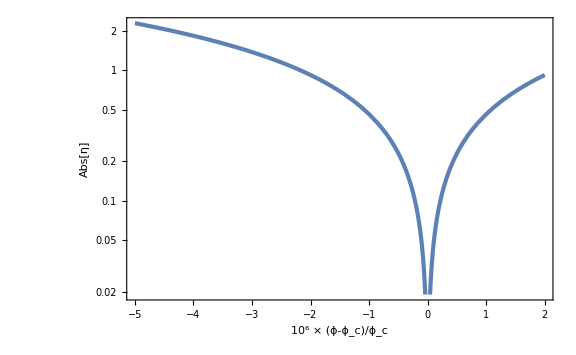

```mathematica
LogPlot[Abs[ηr[ϕc(1+dx 10^-6),0]],{dx,-5,2},GridLines->{None,{2}},FrameLabel->{Row[{"10^6 × ",(ϕ-Subscript[ϕ, "c"])/Subscript[ϕ, "c"]}],Abs[η]}]
```

```mathematica
H[x_,ys_,px_,pys_]:=Sqrt[(px^2/2+(pys.pys)/2+V[x,ys])/3]
```

```mathematica
EoMx={ⅆx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](px[NN]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwx[NN]),
ⅆpx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3px[NN]-D[V[x[NN],ysN], x[NN]]/H[x[NN],ysN,px[NN],pysN])ⅆNN};
EoMy=Flatten[Table[{ⅆysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](pysN[[i]]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwys[[i]][NN]),
ⅆpysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3pysN[[i]]-D[V[x[NN],ysN], ysN[[i]]]/H[x[NN],ysN,px[NN],pysN])ⅆNN},{i,ny}]];
```

```mathematica
IV=Flatten[{ϕc+15/μ1,0,Table[ψr,{i,ny}],Table[0,{i,ny}],0}];
```

```mathematica
prob=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Flatten[{x[NN],px[NN],ysN,pysN,Ninf[NN]}],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
```

```mathematica
Nf=40;
sample=RandomFunction[prob,{0,Nf,0.01}];
```

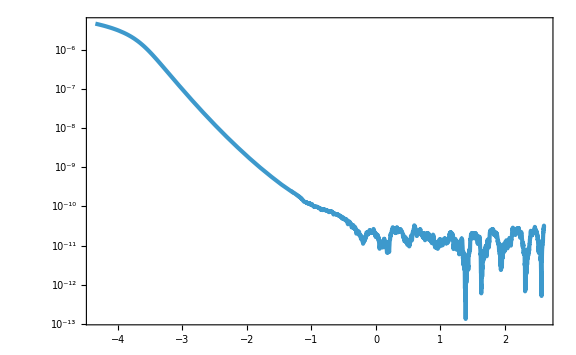

```mathematica
ParametricPlot[{(sample["PathFunction"][NN][[1]]-ϕc)/ϕc 10^6,Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]/M},{NN,0,Nf},ScalingFunctions->{"Linear","Log"}]
```

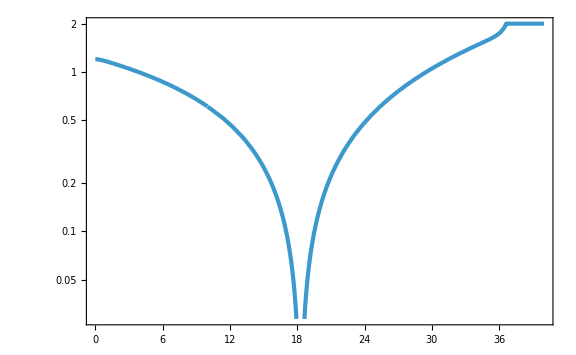

```mathematica
LogPlot[Abs[ηr[sample["PathFunction"][NN][[1]],Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]]],{NN,0,Nf}]//Quiet
```

```mathematica
deltaN=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Ninf[NN],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
Nf=45;
dNsampling=ParallelTable[RandomFunction[deltaN,{0,Nf,0.01},10^3]["LastValues"],{i,10^2}]//Flatten;//AbsoluteTiming
```

{500.514,Null}

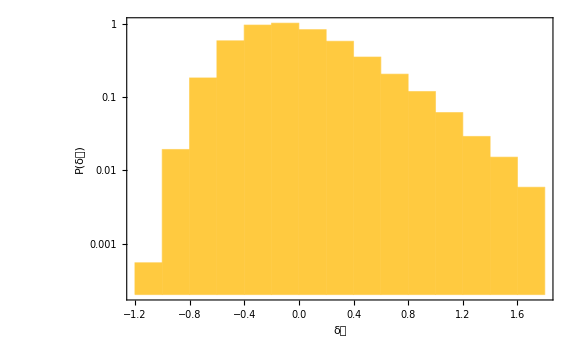

```mathematica
Histogram[dNsampling-Mean[dNsampling],Automatic,{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,"waterfall = 2"}}]
```

### N = 15

```mathematica
ys={y1,y2,y3,y4,y5,y6,y7,y8,y9,y10,y11,y12,y13,y14,y15};
pys={py1,py2,py3,py4,py5,py6,py7,py8,py9,py10,py11,py12,py13,py14,py15};
wys={wy1,wy2,wy3,wy4,wy5,wy6,wy7,wy8,wy9,wy10,wy11,wy12,wy13,wy14,wy15};
ny=Length[ys];
ysN=Table[ys[[i]][NN],{i,ny}];
pysN=Table[pys[[i]][NN],{i,ny}];
```

```mathematica
V[x_,ys_]:=Λ^4((1-(ys.ys)/M^2)^2+2(x^2 ys.ys)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2)
```

```mathematica
Vr[x_,yr_]=Λ^4((1-yr^2/M^2)^2+2(x^2 yr^2)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
ηr[x_,yr_]=D[D[Vr[x,yr], yr], yr]/Vr[x,yr];
```

```mathematica
H[x_,ys_,px_,pys_]:=Sqrt[(px^2/2+(pys.pys)/2+V[x,ys])/3]
```

```mathematica
EoMx={ⅆx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](px[NN]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwx[NN]),
ⅆpx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3px[NN]-D[V[x[NN],ysN], x[NN]]/H[x[NN],ysN,px[NN],pysN])ⅆNN};
EoMy=Flatten[Table[{ⅆysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](pysN[[i]]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwys[[i]][NN]),
ⅆpysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3pysN[[i]]-D[V[x[NN],ysN], ysN[[i]]]/H[x[NN],ysN,px[NN],pysN])ⅆNN},{i,ny}]];
```

```mathematica
IV=Flatten[{ϕc+15/μ1,0,Table[ψr,{i,ny}],Table[0,{i,ny}],0}];
```

```mathematica
prob=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Flatten[{x[NN],px[NN],ysN,pysN,Ninf[NN]}],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
```

```mathematica
Nf=40;
sample=RandomFunction[prob,{0,Nf,0.01}];
```

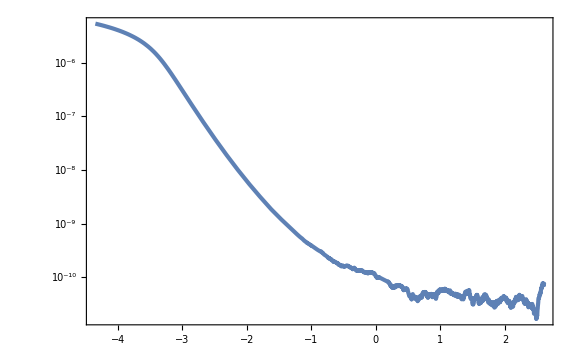

```mathematica
ParametricPlot[{(sample["PathFunction"][NN][[1]]-ϕc)/ϕc 10^6,Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]/M},{NN,0,Nf},ScalingFunctions->{"Linear","Log"}]
```

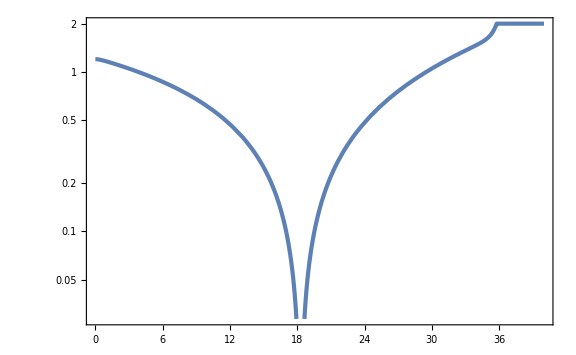

```mathematica
LogPlot[Abs[ηr[sample["PathFunction"][NN][[1]],Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]]],{NN,0,Nf}]//Quiet
```

```mathematica
deltaN=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Ninf[NN],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
Nf=45;
dNsampling=ParallelTable[RandomFunction[deltaN,{0,Nf,0.01},10^3]["LastValues"],{i,10^2}]//Flatten;//AbsoluteTiming
```

{1106.12,Null}

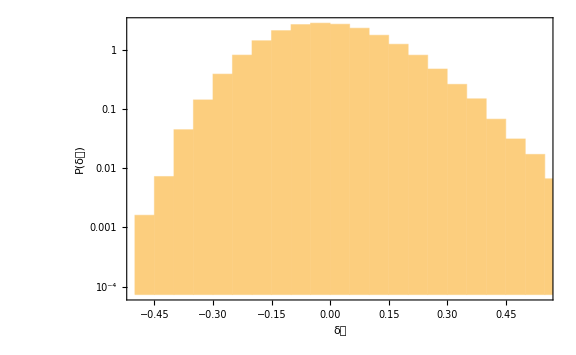

```mathematica
Histogram[dNsampling-Mean[dNsampling],Automatic,{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,"waterfall = 15"}}]
```